# Calculation of LLP particle flux due to cosmic rays (only above 10 GeV COM energy)

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set constants

```mathematica
c = 3*10^8;(*m/s*)
Gf =1.16638*10^(-5); (*GeV^-2*)
```

## Cosmic ray flux

Import cosmic ray flux data from Abe, Koh, et al. “Measurements of cosmic-ray proton and helium spectra from the BESS-Polar long-duration balloon flights over Antarctica.” The Astrophysical Journal 822.2 (2016): 65.

```mathematica
binList = Import["CRKeyVals.csv"];
binList =Delete[binList,1];
energyBins = Table[{binList[[i,2]],binList[[i,4]]},{i,1,Length[binList]}];
energyWidth = Table[binList[[i+69,5]],{i,1,20}];
```

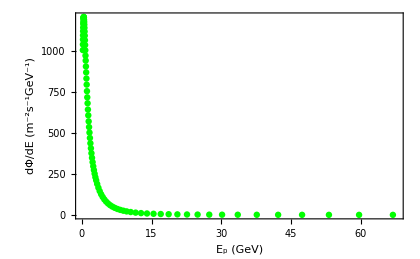

```mathematica
ListPlot[energyBins,FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Green,Thick]]
```

```mathematica
energyBins
```

{{0.206,1004.75},{0.218,1039},{0.231,1069.15},{0.244,1094.75},{0.259,1120},{0.274,1142},{0.29,1164.15},{0.307,1176.45},{0.326,1193.45},{0.345,1200.85},{0.366,1204.5},{0.387,1207.05},{0.41,1206.05},{0.435,1202.45},{0.46,1188.8},{0.487,1176.15},{0.516,1160.3},{0.547,1140.55},{0.579,1118.05},{0.614,1092.75},{0.65,1064.95},{0.688,1035.8},{0.729,1003.7},{0.772,971.1},{0.818,940.8},{0.866,905.05},{0.918,868.9},{0.972,831.4},{1.03,794.3},{1.091,754.35},{1.156,716.65},{1.224,680.6},{1.297,642.2},{1.374,606.95},{1.455,570.05},{1.541,535.55},{1.632,501.95},{1.729,468.9},{1.831,436.6},{1.94,406},{2.054,376.05},{2.176,347.95},{2.305,321.6},{2.442,296.25},{2.587,273.25},{2.74,250.95},{2.902,229.5},{3.074,210.55},{3.289,188.5},{3.551,165.7},{3.834,144.8},{4.14,126},{4.471,109.3},{4.827,94.38},{5.212,81.165},{5.628,69.605},{6.077,59.325},{6.562,50.475},{7.085,42.82},{7.65,36.1},{8.26,30.495},{8.919,25.505},{9.631,21.305},{10.505,17.395},{11.565,13.775},{12.73,10.91},{14.01,8.5975},{15.42,6.7365},{16.97,5.2745},{18.675,4.13},{20.555,3.209},{22.625,2.497},{24.905,1.9275},{27.415,1.4995},{30.175,1.157},{33.55,0.87225},{37.645,0.6363},{42.24,0.4644},{47.395,0.3392},{53.175,0.2481},{59.665,0.1807},{66.945,0.1315},{75.11,0.09677},{84.28,0.07018},{94.565,0.05062},{106.8,0.037575},{121.4,0.02622},{138,0.01871},{156.8,0.013255}}

```mathematica
intEB=Interpolation[energyBins,InterpolationOrder->1]
```

InterpolatingFunction[…]

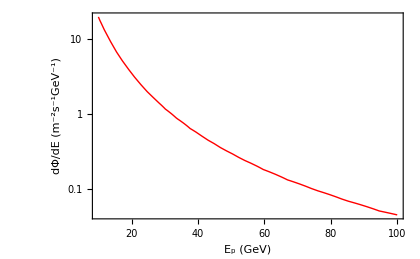

```mathematica
LogPlot[intEB[Ep],{Ep,10,100},FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

## Pythia hadronization

First, we import the kaon results from our 10,000 event pythia runs.

```mathematica
For[i = 1, i <21, i++,  
If[i <10,
kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData0" <>ToString[i]<>".txt"}],"table"];
kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData0" <>ToString[i]<>".txt"}],"table"];kLPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kLPData0" <>ToString[i]<>".txt"}],"table"];
kLNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kLNData0" <>ToString[i]<>".txt"}],"table"],kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData" <>ToString[i]<>".txt"}],"table"];kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData" <>ToString[i]<>".txt"}],"table"];kLPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kLPData" <>ToString[i]<>".txt"}],"table"];
kLNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kLNData" <>ToString[i]<>".txt"}],"table"]
]

]
```

Test nested list element selection

```mathematica
kaonNData[1][[1]]
kaonNData[1][[1,3]]
kaonNData[1][[2]]
kLNData[2][[1]]
```

{Beams:eA,=,18.675}

18.675

{0,3.9598}

{Beams:eA,=,20.555}

Calculate number of kaons produced for a given energy bin

```mathematica
For[i = 1, i <21, i++,  
numPKaons[i]=Times@@Dimensions[kaonPData[i]]-1;
numNKaons[i]=Times@@Dimensions[kaonNData[i]]-1;
numPKLs[i]=Times@@Dimensions[kLPData[i]]-1;
numNKLs[i]=Times@@Dimensions[kLNData[i]]-1;
numKaons[i] = numNKaons[i]+numPKaons[i];
numKLs[i]=numNKLs[i]+numPKLs[i]
]
```

```mathematica
numPKaons[1];
numNKaons[1];
numKaons[2];
numNKLs[2];
numPKLs[2];
numKLs[2];
```

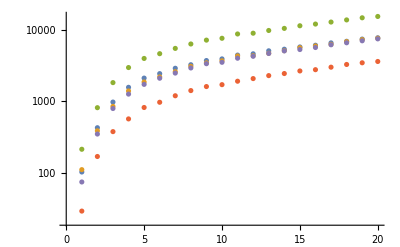

```mathematica
ListLogPlot[{Table[numPKaons[i],{i,1,20}],Table[numNKaons[i],{i,1,20}],Table[numKaons[i],{i,1,20}],Table[numPKLs[i],{i,1,20}],Table[numKLs[i],{i,1,20}]}]
```

Obtain a probability distribution of kaons over energy

### PDF Calculations

```mathematica
For[i = 1, i <21, i++,  
kEngPointsP=Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}];
smoothkEngP =SmoothKernelDistribution[kEngPointsP];
smoothkEng2P =SmoothKernelDistribution[Flatten@kEngPointsP,0.5];
trunkEngP[i] =TruncatedDistribution[{0,1000},smoothkEngP];
trunkEng2P[i] =TruncatedDistribution[{0,1000},smoothkEng2P];
]
For[i = 1, i <21, i++,  
kLEngPointsP=Table[kLPData[i][[j,2]],{j,2,numPKLs[i]+1}];
smoothkLEngP =SmoothKernelDistribution[kLEngPointsP];
smoothkLEng2P =SmoothKernelDistribution[Flatten@kLEngPointsP,0.5];
trunkLEngP[i] =TruncatedDistribution[{0,1000},smoothkLEngP];
trunkLEng2P[i] =TruncatedDistribution[{0,1000},smoothkLEng2P];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPointsN=Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}];
smoothkEngN =SmoothKernelDistribution[kEngPointsN];
smoothkEng2N =SmoothKernelDistribution[Flatten@kEngPointsN,0.5];
trunkEngN[i] =TruncatedDistribution[{0,1000},smoothkEngN];
trunkEng2N[i] =TruncatedDistribution[{0,1000},smoothkEng2N];
]
For[i = 1, i <21, i++,  
kLEngPointsN=Table[kLNData[i][[j,2]],{j,2,numNKLs[i]+1}];
smoothkLEngN =SmoothKernelDistribution[kLEngPointsN];
smoothkLEng2N =SmoothKernelDistribution[Flatten@kLEngPointsN,0.5];
trunkLEngN[i] =TruncatedDistribution[{0,1000},smoothkLEngN];
trunkLEng2N[i] =TruncatedDistribution[{0,1000},smoothkLEng2N];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPoints=Join[Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}],Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}]];
smoothkEng =SmoothKernelDistribution[kEngPoints];
smoothkEng2 =SmoothKernelDistribution[Flatten@kEngPoints,0.5];
trunkEng[i] =TruncatedDistribution[{0,1000},smoothkEng];
trunkEng2[i] =TruncatedDistribution[{0,1000},smoothkEng2];
]
For[i = 1, i <21, i++,  
kLEngPoints=Join[Table[kLNData[i][[j,2]],{j,2,numNKLs[i]+1}],Table[kLPData[i][[j,2]],{j,2,numPKLs[i]+1}]];
smoothkLEng =SmoothKernelDistribution[kLEngPoints];
smoothkLEng2 =SmoothKernelDistribution[Flatten@kLEngPoints,0.5];
trunkLEng[i] =TruncatedDistribution[{0,1000},smoothkLEng];
trunkLEng2[i] =TruncatedDistribution[{0,1000},smoothkLEng2];
]
```

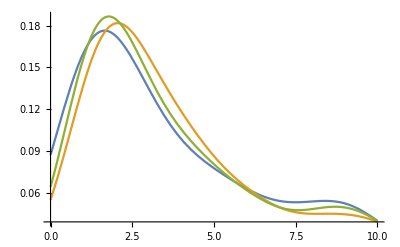

```mathematica
Plot[{PDF[trunkEngP[1],x],PDF[trunkEngN[1],x],PDF[trunkEng[1],x]},{x,0,10}]
```

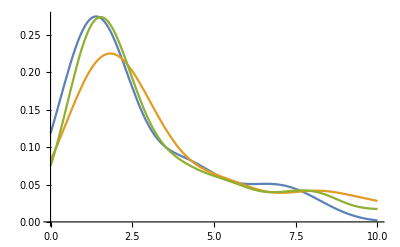

```mathematica
Plot[{PDF[trunkLEngP[1],x],PDF[trunkLEngN[1],x],PDF[trunkLEng[1],x]},{x,0,10}]
```

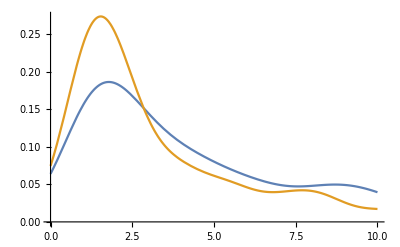

```mathematica
Plot[{PDF[trunkEng[1],x],PDF[trunkLEng[1],x]},{x,0,10}]
```

## LLP flux calculation

The overall form of this expression is: kaon energy distribution X kaons produced per proton X proton flux in a given energy bin

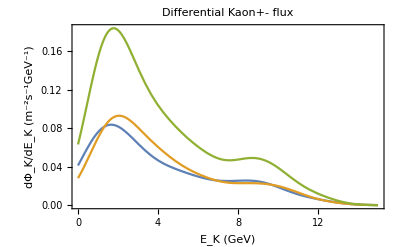

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEngP[1],x]]*numPKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEngN[1],x]]*numNKaons[1]/(2*10^4)*( intEB[
kaonNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon+- flux"]
```

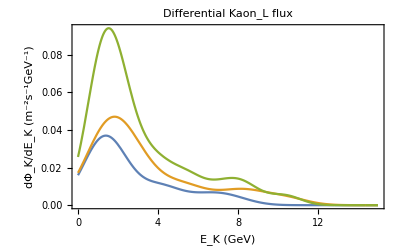

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkLEngP[1],x]]*numPKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEngN[1],x]]*numNKLs[1]/(2*10^4)*( intEB[
kLNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon_L flux"]
```

Combined these! Note: for the purposes of obtaining phi decays (which have a BR 3.5 times higher for K_long than K+-) we can multiply the number of K longs by 3.5 and use the BR of the K+ to determine the phi distribution.

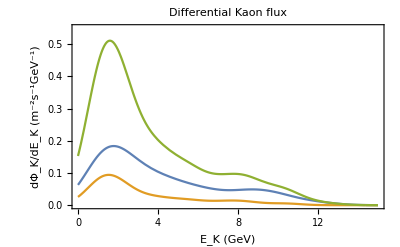

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]]),4Pi*(3.5*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)+Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4))*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotRange-> {0,0.55},PlotLabel->"Differential Kaon flux"]
```

1st line is just one low energy (18 GeV) trial bin, the 2nd is all protons under 30 GeV, the 3rd is all under 50 GeV, the 4th is under 100 GeV, and the final is all energies that the data I’m using has information for.

```mathematica
dKFlux18GeV=4Pi*(3.5*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)+Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4))*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]);
dKFluxSub30=4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,5}];
dKFluxSub50 = 4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,10}];
dKFluxSub100 =4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,16}];
dKFluxAll =4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,11,20}];
dKFluxPlot=4Pi*Sum[(Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}];
```

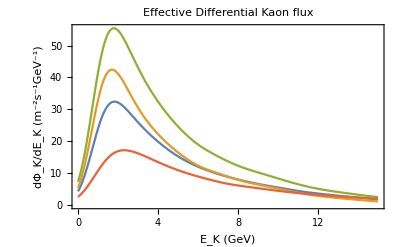

```mathematica
Plot[{(*dKFlux18GeV,dKFluxSub30*)dKFluxPlot,dKFluxSub50,dKFluxSub100,dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Effective Differential Kaon flux"]
```

## Geometry

Here, I introduce all the equations required for the geometry calculations including detector parameters.

```mathematica
L[θ_,R_,h_]:=R*Cos[θ]+Sqrt[h^2 + 2R*h+R^2 *Cos[θ]^2](*In km*)
G[R_,h_]:=N[Integrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))],{θ,0,Pi}]]
```

```mathematica
volSK=Pi*(14.9)^2*32.2;(*In m^3*)
volHK=8*volSK;
```

179667.

Define Kinematic functions:

```mathematica
gamma[phiEng_,mPhi_] :=phiEng/mPhi (*phiEng in GeV*)
velPhi[phiEng_,mPhi_] := Sqrt[1-(1/gamma[phiEng,mPhi]^2 )]*c(*outputs m/s^2*)
disTravel[phiEng_,mPhi_]:=gamma[phiEng,mPhi]*velPhi[phiEng,mPhi]*tauPhi;(*output in m*)
```

```mathematica
detectionTime = 365.25*10*24*3600; (*In s, assuming 10 year detection period*)
```

```mathematica
Gmod[R_,h_,phiEng_,mPhi_]:=NIntegrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))*Exp[-(L[θ,R,h]*1000)/disTravel[phiEng,mPhi]]],{θ,0,Pi}](*This includes the exponential part of the number of events integral*)
```

```mathematica
pointList = Import["llpLifetimePoints.csv"];
pointTable = Table[{pointList[[i,1]],pointList[[i,2]]},{i,1,Length[pointList]}];
intLT = Interpolation[pointTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

## Scalar Kinematics

### Unchanging Inputs

```mathematica
pPhiCM[mPhi_] :=Sqrt[(mKaon^2 -(mPi + mPhi)^2)(mKaon^2 -(mPi - mPhi)^2)]/(2*mKaon);
ePhiCM[mPhi_] := Sqrt[pPhiCM[mPhi]^2 + mPhi^2];
ePhi[mPhi_,eK_,ctheta_] :=(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]ctheta) ;
```

```mathematica
mKaon = 0.4937 ;(*In GeV*)
mPi = 0.1396 ;(*In GeV*)
ms=0.101;
mt=173;
md = 0.005;
CKMfactor = 3.6*10^(-4);
tauK = 1.24*10^(-8)*(1.5192675*10^(24));
```

```mathematica
minEng = 1;(*GeV*)
step=0.15; (*GeV*)
```

```mathematica
totFlux = 0;
For[s = 1, s< (15/step), s++,
x =minEng + (s-1)(step);
totFlux +=dKFluxAll*step;
]
totFlux
```

111.572

Set up output file

```mathematica
PrependTo[CurrentValue[$FrontEndSession,"NotebookPath"],NotebookDirectory[]];
```

```mathematica
titleLine = "Run  mPhi       theta   events" ;
titleLine >>"PhiEventsV6p2.txt"
```

## Need to loop

Currently set to get the last few run finished (post run 6783) this means the angular variable starts at 133 (mixing angle of ~2.2 x 10^-4). Note that I’ve also adjusted the data line so the run number starts from 6784.

```mathematica
angleVar =133;
massVar = 0;
```

```mathematica
{{For[run = 6784, run < 7500, run++,
(*Only put this in for when getting the part 2 runs to avoid the bizarre behaviour for the points with mass = 0.38 Gev*)
If[Mod[run,51]==8,Print["Skipped"],

(*Set ϕ mass and other inputs*)
mPhi = 10^( - (massVar)(0.06)); (*In GeV*)
If[mPhi ≤ 0.2,tauPhiPlot = 10^(-1.116*Log[10,mPhi]+0.4777), tauPhiPlot = intLT[mPhi]];(*In s, from scalar spectator plot*)
mixingAngle = 10^(-1 - (angleVar)(0.02));
tauPhi = tauPhiPlot(10^(-6)/mixingAngle)^2;
minPhiEng = mPhi+0.05; (*Adjust these for final integral over Ephi: must be larger than mPhi*)
engStep = 0.1;

(*Calculate ϕ branching ratio:*)
phiBR = 9*tauK*mixingAngle^2 *Gf^3*mt^4*mKaon^2*CKMfactor^2*pPhiCM[mPhi]/(2048*Sqrt[2]*Pi^5);(*Yue fixed*)
phiBR2 =Sin[mixingAngle]^2 *0.002*2pPhiCM[mPhi]/mKaon ;(*from Arxiv:1310.8042*)

(*Create total probability distribution*)
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
ePhiDist= UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),
(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
truncEPhi[s] =TruncatedDistribution[{0,1000},ePhiDist];
];
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
x =minEng + (s-1)(step);
If[s == 1,totDist = truncEPhi[s],
t = 1;
fluxBelow = 0;
While[t< s,
x=minEng + (t-1)(step);
fluxBelow += dKFluxAll;
t++;
];
x=minEng + (s-1)(step);
fluxAt =dKFluxAll;
totDist=MixtureDistribution[{fluxBelow,fluxAt},{totDist,truncEPhi[s]}]  ]
];
NumberOfEvents=Floor[volHK*detectionTime*
Sum[engStep*Gmod[6400,10,minPhiEng + i*engStep,mPhi]*phiBR*PDF[totDist,minPhiEng+i*engStep]*totFlux/disTravel[minPhiEng+i*engStep,mPhi],
{i,1,149}]];
dataLine =" "<> ToString[run]<>"   "<>ToString[mPhi]<>"   " <>ToString[N[mixingAngle]]<>"  "<>ToString[NumberOfEvents];
PutAppend[dataLine,"PhiEventsV6p2.txt"];

(*end the skip if*)
];
(*Increment variables*)
massVar++;
If[Mod[run,51]== 0,massVar =0;angleVar++;];
If[Mod[run,10] == 0,Print[run]];
];}, {}}
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

6790

Skipped

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.94524616435813}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.094987607675529821260607121757857385091483592987060546875}. NIntegrate obtained 7.40713×10^-319 and 2.5×10^-323 for the integral and error estimates.

General::munfl: 1.20704×10^-305 2.81965×10^-11 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.4578×10^-301 2.81965×10^-11 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.04861039462579}. NIntegrate obtained 1.7257×10^-319 and 3.×10^-323 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 1.20692×10^-304 4.82277×10^-11 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

6800

6810

6820

6830

6840

Skipped

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

6850

6860

6870

6880

6890

Skipped

6900

6910

6920

6930

6940

Skipped

6950

6960

6970

6980

6990

Skipped

7000

7010

7020

7030

7040

Skipped

7050

7060

7070

7080

7090

Skipped

7100

7110

7120

7130

7140

Skipped

7150

7160

7170

7180

7190

Skipped

7200

7210

7220

7230

7240

Skipped

7250

7260

7270

7280

7290

7300

Skipped

7310

7320

7330

7340

$Aborted

```mathematica
massVar =0;
angleVar =0;
```

```mathematica
For[run=1, run<50, run++,

massVar++;
If[Mod[run,21]== 1,massVar =0;angleVar++;];
Print[run," ", massVar," ",angleVar]

]
```

1 0 1

2 1 1

3 2 1

4 3 1

5 4 1

6 5 1

7 6 1

8 7 1

9 8 1

10 9 1

11 10 1

12 11 1

13 12 1

14 13 1

15 14 1

16 15 1

17 16 1

18 17 1

19 18 1

20 19 1

21 20 1

22 0 2

23 1 2

24 2 2

25 3 2

26 4 2

27 5 2

28 6 2

29 7 2

30 8 2

31 9 2

32 10 2

33 11 2

34 12 2

35 13 2

36 14 2

37 15 2

38 16 2

39 17 2

40 18 2

41 19 2

42 20 2

43 0 3

44 1 3

45 2 3

46 3 3

47 4 3

48 5 3

49 6 3

```mathematica
,
```